```mathematica
Qb = a*Et^b
```

a Et^b

```mathematica
scale = (4.0/3.0)*scale0
```

1.33333 scale0

```mathematica
Efac = (1+scale*Qb)/(1+scale)
```

(1+1.33333 a Et^b scale0)/(1+1.33333 scale0)

```mathematica
Subscript[σ, I]= Sqrt[((Subscript[σ, oI])^2 + (Subscript[a, I]*Qb*Et)^2)]
```

√(a^2 Et^(2+2 b) a_ⅈ^2+σ_oI^2)

```mathematica
Subscript[σ, H]= Sqrt[((Subscript[σ, oH])^2 + (Subscript[a, H]*Efac*Et)^2)]
```

√((Et^2 (1+1.33333 a Et^b scale0)^2 a_H^2)/(1+1.33333 scale0)^2+σ_oH^2)

```mathematica
P = (1/Sqrt[Pi*sa])*(1/Sqrt[Pi*sb])*(1/Sqrt[Pi*sc])*(1/Subscript[ϵ, γ])*(1/(1+scale))
```

1/(π^(3/2) √sa √sb √sc (1+1.33333 scale0) ϵ_γ)

```mathematica
fc = P*Abs[Et]*Exp[-(Et - Er)^2/sa]*Exp[-(Er*Qb-Et*Q)^2/sc]
```

(ⅇ^(-(-Er+Et)^2/sa-((a Er Et^b-Et Q)^2)/sc) Abs[Et])/(π^(3/2) √sa √sb √sc (1+1.33333 scale0) ϵ_γ)

```mathematica
fa = ((2*scale*(Et -Er))/sa) + ((2*(Er*Qb-Et*Q))/sc)
```

(2 (a Er Et^b-Et Q))/sc+(2.66667 (-Er+Et) scale0)/sa

```mathematica
fb = (1/sb) + (scale^2/sa) + (1/sc)
```

1/sb+1/sc+(1.77778 scale0^2)/sa

```mathematica
fd = fc*Exp[fa^2/(4*fb)]*(Sqrt[Pi]/Sqrt[fb])*(1/α)*Exp[-α*Er]
```

(ⅇ^(-(-Er+Et)^2/sa-((a Er Et^b-Et Q)^2)/sc+(((2 (a Er Et^b-Et Q))/sc+(2.66667 (-Er+Et) scale0)/sa)^2)/(4 (1/sb+1/sc+(1.77778 scale0^2)/sa))-Er α) Abs[Et])/(π √sa √sb √sc (1+1.33333 scale0) √(1/sb+1/sc+(1.77778 scale0^2)/sa) α ϵ_γ)

```mathematica
Qd = Integrate[fd,{Er,0,Infinity}]
```

ConditionalExpression[(0.211571 ⅇ^(-Et^2/sa-(Et^2 Q^2)/sc+(1. Et^2 Q^2 sa sb)/(sc (1. sa sb+sa sc+1.77778 sb sc scale0^2))-(2.66667 Et^2 Q sb scale0)/(1. sa sb+sa sc+1.77778 sb sc scale0^2)+(1.77778 Et^2 sb sc scale0^2)/(sa (1. sa sb+sa sc+1.77778 sb sc scale0^2))+(1. a^2 Et^(2+2 b) Q^2 sa^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2. a Et^(2+b) Q sa sb)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1. Et^2 sb^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2. a Et^(2+b) Q sa sc)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2. Et^2 sb sc)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1. Et^2 sc^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2.66667 a^2 Et^(2+2 b) Q sa sb scale0)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2.66667 a Et^(2+b) Q^2 sa sb scale0)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2.66667 a Et^(2+b) sb^2 scale0)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2.66667 Et^2 Q sb^2 scale0)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2.66667 a Et^(2+b) sb sc scale0)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2.66667 Et^2 Q sb sc scale0)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(3.55556 a^2 Et^(2+2 b) Q^2 sa sb scale0^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.77778 a^2 Et^(2+2 b) sb^2 scale0^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(7.11111 a Et^(2+b) Q sb^2 scale0^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.77778 Et^2 Q^2 sb^2 scale0^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(3.55556 a Et^(2+b) Q sb sc scale0^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(4.74074 a^2 Et^(2+2 b) Q sb^2 scale0^3)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(4.74074 a Et^(2+b) Q^2 sb^2 scale0^3)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(3.16049 a^2 Et^(2+2 b) Q^2 sb^2 scale0^4)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1. a Et^(1+b) Q sa^2 sb α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1. Et sa sb^2 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1. a Et^(1+b) Q sa^2 sc α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(2. Et sa sb sc α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1. Et sa sc^2 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.33333 a Et^(1+b) sa sb^2 scale0 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.33333 Et Q sa sb^2 scale0 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.33333 a Et^(1+b) sa sb sc scale0 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.33333 Et Q sa sb sc scale0 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.77778 a Et^(1+b) Q sa sb^2 scale0^2 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(3.55556 a Et^(1+b) Q sa sb sc scale0^2 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.77778 Et sb^2 sc scale0^2 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.77778 Et sb sc^2 scale0^2 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(2.37037 a Et^(1+b) sb^2 sc scale0^3 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(2.37037 Et Q sb^2 sc scale0^3 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(3.16049 a Et^(1+b) Q sb^2 sc scale0^4 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(0.25 sa^2 sb^2 α^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(0.5 sa^2 sb sc α^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(0.25 sa^2 sc^2 α^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(0.888889 sa sb^2 sc scale0^2 α^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(0.888889 sa sb sc^2 scale0^2 α^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(0.790123 sb^2 sc^2 scale0^4 α^2)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))) Abs[Et] (1.+1. Erf[(1. a Et^(1+b) Q sa^2 sb √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1. Et sa sb^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1. a Et^(1+b) Q sa^2 sc √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2. Et sa sb sc √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1. Et sa sc^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.33333 a Et^(1+b) sa sb^2 scale0 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.33333 Et Q sa sb^2 scale0 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.33333 a Et^(1+b) sa sb sc scale0 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.33333 Et Q sa sb sc scale0 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.77778 a Et^(1+b) Q sa sb^2 scale0^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(3.55556 a Et^(1+b) Q sa sb sc scale0^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.77778 Et sb^2 sc scale0^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(1.77778 Et sb sc^2 scale0^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2.37037 a Et^(1+b) sb^2 sc scale0^3 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(2.37037 Et Q sb^2 sc scale0^3 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))+(3.16049 a Et^(1+b) Q sb^2 sc scale0^4 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(0.5 sa^2 sb^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)) α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1. sa^2 sb sc √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)) α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(0.5 sa^2 sc^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)) α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.77778 sa sb^2 sc scale0^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)) α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.77778 sa sb sc^2 scale0^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)) α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))-(1.58025 sb^2 sc^2 scale0^4 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)) α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))]))/(√sa √sb √sc (0.75+1. scale0) √(1/sb+1/sc+(1.77778 scale0^2)/sa) √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)) α ϵ_γ),Re[(1. sb+1. sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (1. sa+1.77778 sb scale0^2))/(1. sa sb+1. sa sc+1.77778 sb sc scale0^2)]≥0&&((Re[(-1. sb-1. sc-2.66667 a Et^b sb scale0+a^2 Et^(2 b) (-1. sa-1.77778 sb scale0^2))/(1. sa sb+1. sa sc+1.77778 sb sc scale0^2)]==0&&Re[(Et (2. sb+2. sc+2.66667 Q sb scale0)+a Et^(1+b) (2. Q sa+2.66667 sb scale0+3.55556 Q sb scale0^2)+(-1. sa sb-1. sa sc-1.77778 sb sc scale0^2) α)/(1. sa sb+1. sa sc+1.77778 sb sc scale0^2)]<0)||Re[(-1. sb-1. sc-2.66667 a Et^b sb scale0+a^2 Et^(2 b) (-1. sa-1.77778 sb scale0^2))/(1. sa sb+1. sa sc+1.77778 sb sc scale0^2)]<0)]

```mathematica
Qd_new = Simplify[Qd,{scale ∈ Reals, scale > 0, sa ∈ Reals, sa > 0, sb ∈ Reals, sb>0, sc ∈ Reals, sc ≥ 0, a ∈ Reals, a > 0, b ∈ Reals, b >0, Et ∈ Reals, Et>0, Q ∈ Reals, α ∈ Reals, α > 0}]
```

ConditionalExpression[(ⅇ^((a^2 Et^(2+2 b) (-1. sa sb-1. sa sc-1.77778 sb sc scale0^2)+Et^2 Q^2 (-1. sa sb-1. sa sc-1.77778 sb sc scale0^2)+Et (sb sc scale0^2 (-1.77778 sc+sb (-1.77778-2.37037 Q scale0))+sa (-1. sc^2+sb sc (-2.-1.33333 Q scale0)+sb^2 (-1.-1.33333 Q scale0))) α+(sa^2 (0.25 sb^2+0.5 sb sc+0.25 sc^2)+sa sb (0.888889 sb+0.888889 sc) sc scale0^2+0.790123 sb^2 sc^2 scale0^4) α^2+a Et^(1+b) (Et Q (2. sa sb+2. sa sc+3.55556 sb sc scale0^2)+sb scale0 (-1.33333 sa sb-1.33333 sa sc-2.37037 sb sc scale0^2) α+Q (sa^2 (-1. sb-1. sc)+sa sb (-1.77778 sb-3.55556 sc) scale0^2-3.16049 sb^2 sc scale0^4) α))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))) Et (0.211571+0.211571 Erf[(Et sa (1. sc^2+sb^2 (1.+1.33333 Q scale0)+sb sc (2.+1.33333 Q scale0))+Et sb sc scale0^2 (1.77778 sc+sb (1.77778+2.37037 Q scale0))+a Et^(1+b) (sb scale0 (1.33333 sa sb+1.33333 sa sc+2.37037 sb sc scale0^2)+Q (sa^2 (1. sb+1. sc)+sa sb (1.77778 sb+3.55556 sc) scale0^2+3.16049 sb^2 sc scale0^4))+sa^2 (-0.5 sb^2-1. sb sc-0.5 sc^2) α+sa sb (-1.77778 sb-1.77778 sc) sc scale0^2 α-1.58025 sb^2 sc^2 scale0^4 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2)^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))]))/((0.75+1. scale0) √(1. sb+1. sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (1. sa+1.77778 sb scale0^2)) α ϵ_γ),(1. a^2 Et^(2 b) sa+1. sb+1. sc+2.66667 a Et^b sb scale0+1.77778 a^2 Et^(2 b) sb scale0^2==0&&Et (1. a Et^b Q sa+1. sb+1. sc+1.33333 a Et^b sb scale0+1.33333 Q sb scale0+1.77778 a Et^b Q sb scale0^2)<(0.5 sa sb+0.5 sa sc+0.888889 sb sc scale0^2) α)||1. a^2 Et^(2 b) sa+1. sb+1. sc+2.66667 a Et^b sb scale0+1.77778 a^2 Et^(2 b) sb scale0^2>0]

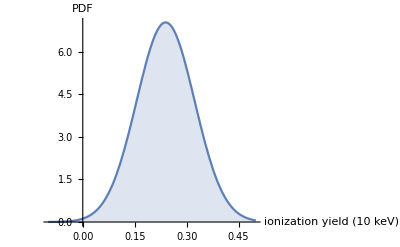

```mathematica
Plot[Simplify[Qd,{sa==0.5,sb==0.5,sc==0.5,Et==10.0,a==0.16,b==0.18,scale0==1.0, α==(1/18.0), Subscript[ϵ, γ] == 3.0}],{Q,-0.1,0.5},Filling->Axis,AxesLabel->{"ionization yield (10 keV)",PDF}]
```

```mathematica
Simplify[Qd,{sa==0.5,sb==0.5,sc==0.5,Et==10.0,a==0.16,b==0.18,scale==1.0, α==(1/18.0)}]
```

(0.151986 ⅇ^((36.9166-76.8748 Q) Q) (1.+Erf[11.329+7.51389 Q]))/ϵ_γ

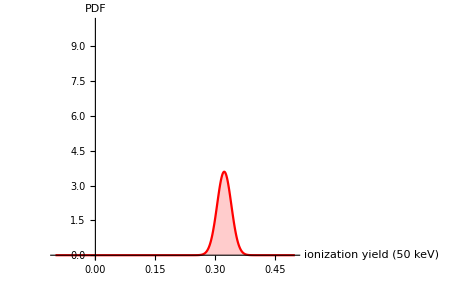

```mathematica
Plot[Simplify[Qd,{sa==0.5,sb==0.5,sc==0.5,Et==50.0,a==0.16,b==0.18,scale0==1.0, α==(1/18.0), Subscript[ϵ, γ]==3.0}],{Q,-0.1,0.5},Filling->Axis,PlotStyle->Red,PlotRange->{{-0.1,0.5},{0,10.0}},AxesLabel->{"ionization yield (50 keV)",PDF}]
```

```mathematica
Integrate[Simplify[Q*Qd,{sa==0.5,sb==0.5,sc==0.5,a==0.16,b==0.18,scale==1.0, P==1, α==(1/18.0)}],{Q,-Infinity,Infinity}]
```

∫_(-∞)^∞ ((2.93162 ⅇ^((0.0036169-0.16 Et^(59/25)+Et^1.18 (-0.0277778-0.0555556 Q)+2. Et^2.18 Q-6.25 Et^2 Q^2-0.173611 Et (2.+Q))/(6.25+Et^0.18+0.16 Et^(9/25))) Q Abs[Et] (1+Erf[(6.25 √(1.33333+0.213333 Et^0.18+0.0341333 Et^0.36) (-0.130208+Et^1.18 (0.5+Q)+3.125 Et (2.+Q)))/(39.0625+6.25 Et^0.18+Et^(9/25))]))/(√(1.33333+0.213333 Et^0.18+0.0341333 Et^0.36) ϵ_γ))ⅆQ

```mathematica
Integrate[Simplify[Q^2*Qd,{sa==0.5,sb==0.5,sc==0.5,a==0.16,b==0.18,scale==1.0, P==1, α==(1/18.0)}],{Q,-Infinity,Infinity}]
```

∫_(-∞)^∞ ((2.93162 ⅇ^((0.0036169-0.16 Et^(59/25)+Et^1.18 (-0.0277778-0.0555556 Q)+2. Et^2.18 Q-6.25 Et^2 Q^2-0.173611 Et (2.+Q))/(6.25+Et^0.18+0.16 Et^(9/25))) Q^2 Abs[Et] (1+Erf[(6.25 √(1.33333+0.213333 Et^0.18+0.0341333 Et^0.36) (-0.130208+Et^1.18 (0.5+Q)+3.125 Et (2.+Q)))/(39.0625+6.25 Et^0.18+Et^(9/25))]))/(√(1.33333+0.213333 Et^0.18+0.0341333 Et^0.36) ϵ_γ))ⅆQ

```mathematica
Simplify[Qd,{scale ∈ Reals, scale > 0, sa ∈ Reals, sa > 0, sb ∈ Reals, sb>0, sc ∈ Reals, sc ≥ 0, a ∈ Reals, a > 0, a< 1, b ∈ Reals, b >0, b<1, Et ∈ Reals, Et>0, Q ∈ Reals, α ∈ Reals, α > 0}]
```

ConditionalExpression[(ⅇ^((a^2 Et^(2+2 b) (-1. sa sb-1. sa sc-1.77778 sb sc scale0^2)+Et^2 Q^2 (-1. sa sb-1. sa sc-1.77778 sb sc scale0^2)+Et (sb sc scale0^2 (-1.77778 sc+sb (-1.77778-2.37037 Q scale0))+sa (-1. sc^2+sb sc (-2.-1.33333 Q scale0)+sb^2 (-1.-1.33333 Q scale0))) α+(sa^2 (0.25 sb^2+0.5 sb sc+0.25 sc^2)+sa sb (0.888889 sb+0.888889 sc) sc scale0^2+0.790123 sb^2 sc^2 scale0^4) α^2+a Et^(1+b) (Et Q (2. sa sb+2. sa sc+3.55556 sb sc scale0^2)+sb scale0 (-1.33333 sa sb-1.33333 sa sc-2.37037 sb sc scale0^2) α+Q (sa^2 (-1. sb-1. sc)+sa sb (-1.77778 sb-3.55556 sc) scale0^2-3.16049 sb^2 sc scale0^4) α))/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2) (1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2)))) Et (0.211571+0.211571 Erf[(Et sa (1. sc^2+sb^2 (1.+1.33333 Q scale0)+sb sc (2.+1.33333 Q scale0))+Et sb sc scale0^2 (1.77778 sc+sb (1.77778+2.37037 Q scale0))+a Et^(1+b) (sb scale0 (1.33333 sa sb+1.33333 sa sc+2.37037 sb sc scale0^2)+Q (sa^2 (1. sb+1. sc)+sa sb (1.77778 sb+3.55556 sc) scale0^2+3.16049 sb^2 sc scale0^4))+sa^2 (-0.5 sb^2-1. sb sc-0.5 sc^2) α+sa sb (-1.77778 sb-1.77778 sc) sc scale0^2 α-1.58025 sb^2 sc^2 scale0^4 α)/((1. sa sb+1. sa sc+1.77778 sb sc scale0^2)^2 √((1. sb+sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (sa+1.77778 sb scale0^2))/(1. sa sb+sa sc+1.77778 sb sc scale0^2)))]))/((0.75+1. scale0) √(1. sb+1. sc+2.66667 a Et^b sb scale0+a^2 Et^(2 b) (1. sa+1.77778 sb scale0^2)) α ϵ_γ),(1. a^2 Et^(2 b) sa+1. sb+1. sc+2.66667 a Et^b sb scale0+1.77778 a^2 Et^(2 b) sb scale0^2==0&&Et (1. a Et^b Q sa+1. sb+1. sc+1.33333 a Et^b sb scale0+1.33333 Q sb scale0+1.77778 a Et^b Q sb scale0^2)<(0.5 sa sb+0.5 sa sc+0.888889 sb sc scale0^2) α)||1. a^2 Et^(2 b) sa+1. sb+1. sc+2.66667 a Et^b sb scale0+1.77778 a^2 Et^(2 b) sb scale0^2>0]